```mathematica
2-2
```

0

```mathematica
Energetics of Torn Membranes
```

Nicholas Wheeler
Reed College Physics Department
7 October 2009

### Objective

Let a set of points on the plane be connected by unstretched springs. Asssign "unnatural" coordinates to one or more of the boundary points. Interior points will reposition themselves so as to minimize the potential energy of the system. Snip a spring. Again the points reposition themselves, arriving at a configuration with energy lower than it was before. I propose to develop simple realizations of such systems. I begin with a system of the following initial (unstressed) design:

```mathematica
Points=Table[{i,j},{i,1,4},{j,1,3}]
```

{{{1,1},{1,2},{1,3}},{{2,1},{2,2},{2,3}},{{3,1},{3,2},{3,3}},{{4,1},{4,2},{4,3}}}

```mathematica
Table[Subscript[P, i,j]=Points⟦i⟧⟦j⟧,{i,1,4},{j,1,3}]
```

{{{1,1},{1,2},{1,3}},{{2,1},{2,2},{2,3}},{{3,1},{3,2},{3,3}},{{4,1},{4,2},{4,3}}}

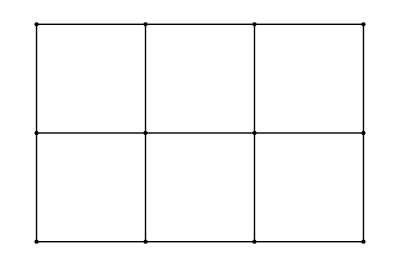

```mathematica
Graphics[{{PointSize[Large],Point[{Subscript[P, 1,1],Subscript[P, 2,1],Subscript[P, 3,1],Subscript[P, 4,1],
Subscript[P, 1,2],Subscript[P, 2,2],Subscript[P, 3,2],Subscript[P, 4,2],
Subscript[P, 1,3],Subscript[P, 2,3],Subscript[P, 3,3],Subscript[P, 4,3]}]},
Line[{{Subscript[P, 1,1],Subscript[P, 2,1],Subscript[P, 3,1],Subscript[P, 4,1]},{Subscript[P, 1,2],Subscript[P, 2,2],Subscript[P, 3,2],Subscript[P, 4,2]},{Subscript[P, 1,3],Subscript[P, 2,3],Subscript[P, 3,3],Subscript[P, 4,3]},
{Subscript[P, 1,1],Subscript[P, 1,2],Subscript[P, 1,3]},
{Subscript[P, 2,1],Subscript[P, 2,2],Subscript[P, 2,3]},
{Subscript[P, 3,1],Subscript[P, 3,2],Subscript[P, 3,3]},
{Subscript[P, 4,1],Subscript[P, 4,2],Subscript[P, 4,3]}}]}]
```

### Energy stored in a stretched connection spring

REMARK: This discussion is taken from page 34 in Chapter 3 of my Classical Mechanics II notes (2004).

Proceeding in reference to the following figure

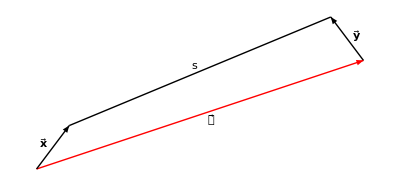

```mathematica
Graphics[{{Thick,Red,{Arrow[{{0,0},{3,1}}]}},
{Thick,{Arrow[{{0,0},{.3,.4}}]}},
{Thick,{Arrow[{{3,1},{3-.3,1+.4}}]}},
{Line[{{.3,.4},{3-.3,1+.4}}]},
Text[Style["𝒶⃗",Bold,Larger],{1.6,.45}],
Text[Style["x⃗",Bold,Larger],{.06,.23}],
Text[Style["y⃗",Bold,Larger],{2.94,1.23}],
Text[Style["s",Larger],{1.45,.95}]}]
```

The red  a⃗-vector refers to a relaxed spring of length 𝒶. Infinitesimal displacements x⃗ and y⃗ of its respective ends cause the spring to have altered length

```mathematica
𝓈=√((a⃗+y⃗-x⃗).(a⃗+y⃗-x⃗))
=𝒶 √(1+(2 a⃗.(y⃗-x⃗)+(y⃗-x⃗).(y⃗-x⃗))/𝒶)
=𝒶 + ((a⃗)/𝒶).(y⃗-x⃗)+⋯
```

The potential energy stored in the distorted spring is

```mathematica
U=1/2 k (𝓈-𝒶)^2
```

which in leading order has become

```mathematica
U=1/2 k(((a⃗)/𝒶).(y⃗-x⃗))^2
```

where (a⃗)/𝒶 is the unit vector defined by the undisturbed spring.

### Application to the system at hand

To minimize notational clutter, we might be tempted to assume initially that the particles are free to move only laterally (i.e., in the x-direction). The excursion variables would then only 12 in number: x_(i,j) where

```mathematica
i ∈ {1,2,3,4}
j ∈ {1,2,3}
```

But it is my impression that the physics would then be too simple to be interesting (meaning to display the effects in which I have interest). I will allow relaxation motion to include also y-adjustments, and have therefore to contend with a total of 24 variables:

```mathematica
Subscript[({{x}, {y}}), i,j]
```

I henceforth dispense with the commas in the subscripts.

Because of the square-lattice design of our "crystal/membrane" we have only two unit displacement vectors to contend with:

```mathematica
h=({{1}, {0}});
v=({{0}, {1}});
```

where the notation is intended to suggest horizontal and vertical.

The energy stored in the horizontal spring at lower left is given now by

```mathematica
(1/2 k (Transpose[h].({{Subscript[x, 21]-Subscript[x, 11]}, {Subscript[y, 21]-Subscript[y, 11]}}))^2)⟦1⟧⟦1⟧
```

1/2 k (-x_11+x_21)^2

and the energy stored in the entire population of horizontal springs (if we assume all such spring constants to be the same) is given by

```mathematica
Subscript[U, horizontal]=1/2 k (Subscript[x, 21]-Subscript[x, 11])^2+1/2 k (Subscript[x, 31]-Subscript[x, 21])^2+1/2 k (Subscript[x, 41]-Subscript[x, 31])^2+1/2 k (Subscript[x, 22]-Subscript[x, 12])^2+1/2 k (Subscript[x, 32]-Subscript[x, 22])^2+1/2 k (Subscript[x, 42]-Subscript[x, 32])^2+1/2 k (Subscript[x, 23]-Subscript[x, 13])^2+1/2 k (Subscript[x, 33]-Subscript[x, 23])^2+1/2 k (Subscript[x, 43]-Subscript[x, 33])^2;
```

for which I have constructed—and now test

```mathematica
Simplify[Subscript[U, horizontal]-(k/2 Transpose[({{Subscript[x, 11]}, {Subscript[x, 21]}, {Subscript[x, 31]}, {Subscript[x, 41]}, {Subscript[x, 12]}, {Subscript[x, 22]}, {Subscript[x, 32]}, {Subscript[x, 42]}, {Subscript[x, 13]}, {Subscript[x, 23]}, {Subscript[x, 33]}, {Subscript[x, 43]}})].({{1, -1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {-1, 2, -1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, -1, 2, -1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, -1, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, -1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, -1, 2, -1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, -1, 2, -1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, -1, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, -1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, -1, 2, -1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, -1, 2, -1}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -1, 1}}).({{Subscript[x, 11]}, {Subscript[x, 21]}, {Subscript[x, 31]}, {Subscript[x, 41]}, {Subscript[x, 12]}, {Subscript[x, 22]}, {Subscript[x, 32]}, {Subscript[x, 42]}, {Subscript[x, 13]}, {Subscript[x, 23]}, {Subscript[x, 33]}, {Subscript[x, 43]}}))⟦1⟧⟦1⟧]
```

0

—a matrix formulation. Notice that every row/column in the matrix sums to zero.

For the vertical spring in the lower left we have (if we assume those springs to have spring constant g—perhaps different from k)

```mathematica
(1/2 g (Transpose[v].({{Subscript[x, 12]-Subscript[x, 11]}, {Subscript[y, 12]-Subscript[y, 11]}}))^2)⟦1⟧⟦1⟧
```

1/2 g (-y_11+y_12)^2

so the total energy stored in the vertical springs is

```mathematica
Subscript[U, vertical]=1/2 g (Subscript[y, 12]-Subscript[y, 11])^2+1/2 g (Subscript[y, 13]-Subscript[y, 12])^2+1/2 g (Subscript[y, 22]-Subscript[y, 21])^2+1/2 g (Subscript[y, 23]-Subscript[y, 22])^2+1/2 g (Subscript[y, 32]-Subscript[y, 31])^2+1/2 g (Subscript[y, 33]-Subscript[y, 32])^2+1/2 g (Subscript[y, 42]-Subscript[y, 41])^2+1/2 g (Subscript[y, 43]-Subscript[y, 42])^2;
```

```mathematica
-2 Subscript[y, 12] Subscript[y, 13]-2 Subscript[y, 21] Subscript[y, 22]-2 Subscript[y, 22] Subscript[y, 23]-2 Subscript[y, 31] Subscript[y, 32]-2 Subscript[y, 32] Subscript[y, 33]-2 Subscript[y, 41] Subscript[y, 42]-2 Subscript[y, 42] Subscript[y, 43]
```

which again we are able to write in matrix form:

```mathematica
Simplify[Subscript[U, vertical]-g/2(Transpose[({{Subscript[y, 11]}, {Subscript[y, 21]}, {Subscript[y, 31]}, {Subscript[y, 41]}, {Subscript[y, 12]}, {Subscript[y, 22]}, {Subscript[y, 32]}, {Subscript[y, 42]}, {Subscript[y, 13]}, {Subscript[y, 23]}, {Subscript[y, 33]}, {Subscript[y, 43]}})].({{1, 0, 0, 0, -1, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, -1, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, -1, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, -1, 0, 0, 0, 0}, {-1, 0, 0, 0, 2, 0, 0, 0, -1, 0, 0, 0}, {0, -1, 0, 0, 0, 2, 0, 0, 0, -1, 0, 0}, {0, 0, -1, 0, 0, 0, 2, 0, 0, 0, -1, 0}, {0, 0, 0, -1, 0, 0, 0, 2, 0, 0, 0, -1}, {0, 0, 0, 0, -1, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, -1, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, -1, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, -1, 0, 0, 0, 1}}).({{Subscript[y, 11]}, {Subscript[y, 21]}, {Subscript[y, 31]}, {Subscript[y, 41]}, {Subscript[y, 12]}, {Subscript[y, 22]}, {Subscript[y, 32]}, {Subscript[y, 42]}, {Subscript[y, 13]}, {Subscript[y, 23]}, {Subscript[y, 33]}, {Subscript[y, 43]}}))⟦1⟧⟦1⟧]
```

0

Once again, all rows/columns sum to zero.

```mathematica
Eigenvalues[({{1, -1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {-1, 2, -1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, -1, 2, -1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, -1, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, -1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, -1, 2, -1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, -1, 2, -1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, -1, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, -1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, -1, 2, -1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, -1, 2, -1}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -1, 1}})]//N
```

{3.41421,3.41421,3.41421,2.,2.,2.,0.585786,0.585786,0.585786,0.,0.,0.}

```mathematica
Eigenvalues[({{1, 0, 0, 0, -1, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, -1, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, -1, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, -1, 0, 0, 0, 0}, {-1, 0, 0, 0, 2, 0, 0, 0, -1, 0, 0, 0}, {0, -1, 0, 0, 0, 2, 0, 0, 0, -1, 0, 0}, {0, 0, -1, 0, 0, 0, 2, 0, 0, 0, -1, 0}, {0, 0, 0, -1, 0, 0, 0, 2, 0, 0, 0, -1}, {0, 0, 0, 0, -1, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, -1, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, -1, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, -1, 0, 0, 0, 1}})]//N
```

{3.,3.,3.,3.,1.,1.,1.,1.,0.,0.,0.,0.}

```mathematica
({{a, b, 0, 0}, {c, d, 0, 0}, {0, 0, p, q}, {0, 0, r, s}})
```

{{a,b,0,0},{c,d,0,0},{0,0,p,q},{0,0,r,s}}

```mathematica
Det[%]
```

b c q r-a d q r-b c p s+a d p s

```mathematica
Simplify[%]
```

(b c-a d) (q r-p s)